# Lab 10: Mathematica Practice

## Problem 1: Basic Computation (Basic Syntax)

In a new notebook, make a section (choose your own formatting) and write the code to do these computations.

(a.)

```mathematica
(1+(2/(3-Log10[4])))^(1/2);
N[%,10]
```

1.354270735

(b.) The answer to (a.)

```mathematica
%+Log[2.39]
```

2.22556

## Problem 2: Mathematical Operations with Lists

(a.) and (b.)

```mathematica
x={-1.2,-0.4,0.4,1.2,2,2.8,3.6};
y=((2*x^2-16*x+4)^2)/(x+15)
```

{49.2874,7.87112,0.280935,9.36928,400/17,35.4502,41.1926}

## Problem 3: Solving an equation, numerically

(a .)

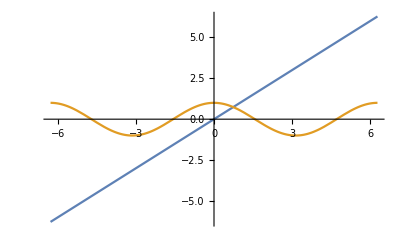

```mathematica
Clear[x];
Plot[{x,Cos[x]},{x,-2*π,2*π}]
```

(b.)

```mathematica
FindRoot[0==Cos[x]-x,{x,π}]
```

{x→0.739085}

## Problem 4: Two summations

(a.)

```mathematica
Sum[1/n^6,{n,1,∞}]
N[%]
```

π^6/945

1.01734

(b.)

```mathematica
Sum[(-1)^n/n,{n,1,∞}]
N[%]
```

-Log[2]

-0.693147

## Problem 5: Preform two multivariate integrals

(a .)

```mathematica
Clear[x,y];
∫∫Sin[x*y]ⅆxⅆy

Plot3D[Sin[x*y],{x,0,2*π},{y,0,2*π}]
```

-CosIntegral[x y]

-Graphics3D-

(b.)

```mathematica
Clear[x,y];
∫_-2^2 ∫_-2^2 (x^2+y^2)ⅆxⅆy
```

128/3

## Problem 6: A physics example, LRC Bandpass Filter

(a.)

```mathematica
(*Inductance [Henrys]*)
L=25*10^-3;
(*Capacitance [Farads]*)
c=10*10^-9;
(*Resistance [Ohms]*)
R=1*10^4;
Gain[f_,L_,c_,R_]:=(2*π*f*L)/(((2*π*f*L)^2+(R-(2*π*f)^2*R*L*c)^2)^(1/2));
```

(b.)

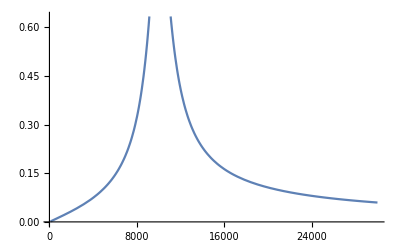

```mathematica
Plot[Gain[f,L,c,R],{f,100,30*10^3}]
```

(c.)

```mathematica
Manipulate[
Plot[Gain[f,L,c,R],{f,100,30*10^3}],
{L,10*10^-3,50*10^-3},
{c,2*10^-9,20*10^-9},
{R,3*10^3,2*10^4}]
```

(d.)
The inductance, L, moves the peak. As L increases the peak position decreases and as L decreases the peak position increases. They are inversely correlated.
The capacitance, c, effects the width of the distribution and its position. As c increases the peak becomes tighter and its position decreases. As c decreases the peak position increases and becomes broader.
The resistance, R, effects the width of the distribution without moving the distribution. Increasing R tightens the distribution and decreasing R broadens the distribution.
There exists a relationship between the three. At some related values the distribution peaks at 1 and tends to remain there for some range of values. At some particular points the distribution suddenly becomes peaked at values greater than 1.

## Problem 7: Pendulum

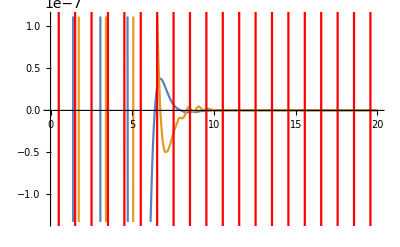

```mathematica
ClearAll["Global`*"];

(*define terms*)
(*acceleration of gravity [m/s^2]*)
g=9.8;
(*length of pendulum [m]*)
l=1;
(*final simulation time [s]*)
tf=20;
(*initial pendulum angle [radians]*)
θi=40*π/180;
(*damping coefficient [ ]*)
γ=5;

(*solve the 2nd order ODE*)
eq1=y''[t]==-g*Sin[y[t]]/l-γ*y'[t];
eq2=y'[0]==0;
eq3=y[0]==θi;
s=NDSolve[{eq1,eq2,eq3},{y,y'},{t,0,tf}];

(*replace rules solution with functions*)
{θ[t_],ω[t_]}={y[t],y'[t]}/.s//Flatten;

(*plot angular position and velocity and approximate*)
plot1=Plot[{θ[t],ω[t]},{t,0,tf}];
plot2=Plot[θi*Cos[Sqrt[g/l]*t],{t,0,tf},PlotStyle->{Red}];
Show[plot1,plot2]

(*find x,y position for graphics*)
x[t_]=l*Sin[θ[t]];
y[t_]=-l*Cos[θ[t]];

(*make an animation of the pendulum motion*)
Animate[
Graphics[
{
Disk[{x[t],y[t]},0.05],
Line[{{0,0},{x[t],y[t]}}]
},
PlotRange->{{-1.5,1.5},{-1,0}}],
{t,0,tf},
AnimationRate->0.3]
```

It is hard to tell the difference between critically damped and overdamped.

### No Damp

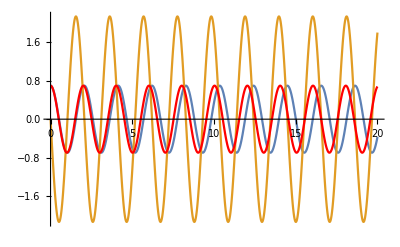

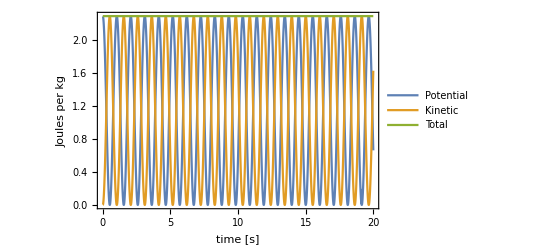

```mathematica
ClearAll["Global`*"];

(*define terms*)
(*acceleration of gravity [m/s^2]*)
g=9.8;
(*length of pendulum [m]*)
l=1;
(*final simulation time [s]*)
tf=20;
(*initial pendulum angle [radians]*)
θi=40*π/180;
(*damping coefficient [ ]*)
γ=0;

(*solve the 2nd order ODE*)
eq1=y''[t]==-g*Sin[y[t]]/l-γ*y'[t];
eq2=y'[0]==0;
eq3=y[0]==θi;
s=NDSolve[{eq1,eq2,eq3},{y,y'},{t,0,tf}];

(*replace rules solution with functions*)
{θ[t_],ω[t_]}={y[t],y'[t]}/.s//Flatten;

(*plot angular position and velocity and approximate*)
plot1=Plot[{θ[t],ω[t]},{t,0,tf}];
plot2=Plot[θi*Cos[Sqrt[g/l]*t],{t,0,tf},PlotStyle->{Red}];
Show[plot1,plot2]

(*find x,y position for graphics*)
x[t_]=l*Sin[θ[t]];
y[t_]=-l*Cos[θ[t]];

(*make an animation of the pendulum motion*)
Animate[
Graphics[
{
Disk[{x[t],y[t]},0.05],
Line[{{0,0},{x[t],y[t]}}]
},
PlotRange->{{-1.5,1.5},{-1,0}}],
{t,0,tf},
AnimationRate->0.3]

(*plot the potential, kinetic, and total energy*)
U[h_]=g*(h+l);
KE[v_]=1/2*v^2;
Etot[h_,v_]=U[h]+KE[v];
Plot[
{U[y[t]],KE[ω[t]*l],Etot[y[t],ω[t]*l]},
{t,0,tf},
Frame->True,
FrameLabel->{"time [s]","Joules per kg"},
PlotLegends->{"Potential","Kinetic","Total"}
]
```

### Moderate damping

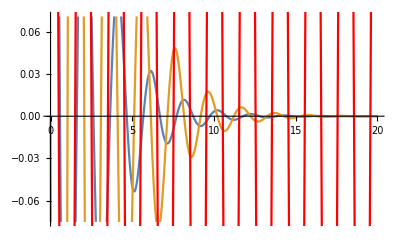

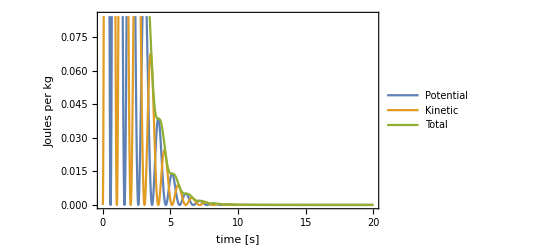

```mathematica
ClearAll["Global`*"];

(*define terms*)
(*acceleration of gravity [m/s^2]*)
g=9.8;
(*length of pendulum [m]*)
l=1;
(*final simulation time [s]*)
tf=20;
(*initial pendulum angle [radians]*)
θi=40*π/180;
(*damping coefficient [ ]*)
γ=1;

(*solve the 2nd order ODE*)
eq1=y''[t]==-g*Sin[y[t]]/l-γ*y'[t];
eq2=y'[0]==0;
eq3=y[0]==θi;
s=NDSolve[{eq1,eq2,eq3},{y,y'},{t,0,tf}];

(*replace rules solution with functions*)
{θ[t_],ω[t_]}={y[t],y'[t]}/.s//Flatten;

(*plot angular position and velocity and approximate*)
plot1=Plot[{θ[t],ω[t]},{t,0,tf}];
plot2=Plot[θi*Cos[Sqrt[g/l]*t],{t,0,tf},PlotStyle->{Red}];
Show[plot1,plot2]

(*find x,y position for graphics*)
x[t_]=l*Sin[θ[t]];
y[t_]=-l*Cos[θ[t]];

(*make an animation of the pendulum motion*)
Animate[
Graphics[
{
Disk[{x[t],y[t]},0.05],
Line[{{0,0},{x[t],y[t]}}]
},
PlotRange->{{-1.5,1.5},{-1,0}}],
{t,0,tf},
AnimationRate->0.3]

(*plot the potential, kinetic, and total energy*)
U[h_]=g*(h+l);
KE[v_]=1/2*v^2;
Etot[h_,v_]=U[h]+KE[v];
Plot[
{U[y[t]],KE[ω[t]*l],Etot[y[t],ω[t]*l]},
{t,0,tf},
Frame->True,
FrameLabel->{"time [s]","Joules per kg"},
PlotLegends->{"Potential","Kinetic","Total"}
]
```

### Critical Damping

-Graphics-

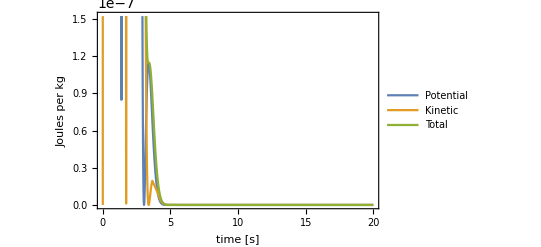

```mathematica
ClearAll["Global`*"];

(*define terms*)
(*acceleration of gravity [m/s^2]*)
g=9.8;
(*length of pendulum [m]*)
l=1;
(*final simulation time [s]*)
tf=20;
(*initial pendulum angle [radians]*)
θi=40*π/180;
(*damping coefficient [ ]*)
γ=5;

(*solve the 2nd order ODE*)
eq1=y''[t]==-g*Sin[y[t]]/l-γ*y'[t];
eq2=y'[0]==0;
eq3=y[0]==θi;
s=NDSolve[{eq1,eq2,eq3},{y,y'},{t,0,tf}];

(*replace rules solution with functions*)
{θ[t_],ω[t_]}={y[t],y'[t]}/.s//Flatten;

(*plot angular position and velocity and approximate*)
plot1=Plot[{θ[t],ω[t]},{t,0,tf}];
plot2=Plot[θi*Cos[Sqrt[g/l]*t],{t,0,tf},PlotStyle->{Red}];
Show[plot1,plot2]

(*find x,y position for graphics*)
x[t_]=l*Sin[θ[t]];
y[t_]=-l*Cos[θ[t]];

(*make an animation of the pendulum motion*)
Animate[
Graphics[
{
Disk[{x[t],y[t]},0.05],
Line[{{0,0},{x[t],y[t]}}]
},
PlotRange->{{-1.5,1.5},{-1,0}}],
{t,0,tf},
AnimationRate->0.3]

(*plot the potential, kinetic, and total energy*)
U[h_]=g*(h+l);
KE[v_]=1/2*v^2;
Etot[h_,v_]=U[h]+KE[v];
Plot[
{U[y[t]],KE[ω[t]*l],Etot[y[t],ω[t]*l]},
{t,0,tf},
Frame->True,
FrameLabel->{"time [s]","Joules per kg"},
PlotLegends->{"Potential","Kinetic","Total"}
]
```